# 3.1

a)

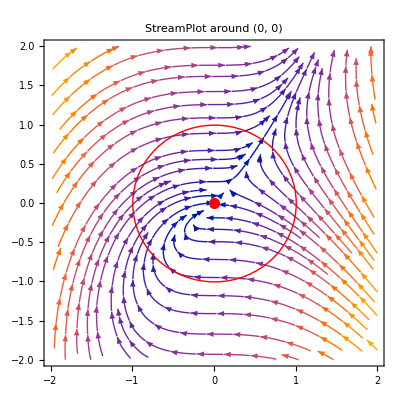

```mathematica
fixedPoint={0,0};
radius=1;

StreamPlot[{y-x,x^2},{x,-2,2},{y,-2,2},PlotLabel->"StreamPlot around (0, 0)",Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
```

Index =0
b)

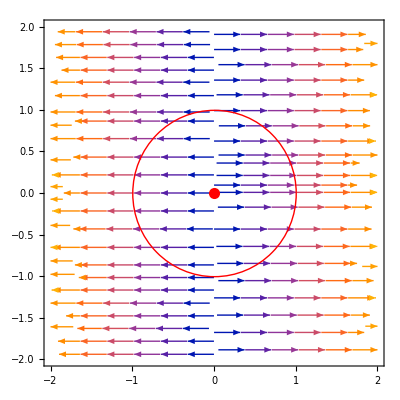

```mathematica
h[r_]:=a*r; (*Define the function h(r)*)
a=0.5; (*Define the value of'a'*)

fixedPoint={0,0};
radius=1;

StreamPlot[{h[r],0},{r,-2,2},{θ,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
```

Index = 1  for  b)

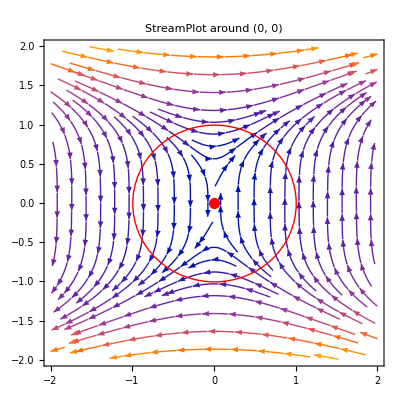

```mathematica
fixedPoint={0,0};
radius=1;

StreamPlot[{y^3,x},{x,-2,2},{y,-2,2},PlotLabel->"StreamPlot around (0, 0)",Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
```

Index =-1 
d)

-2

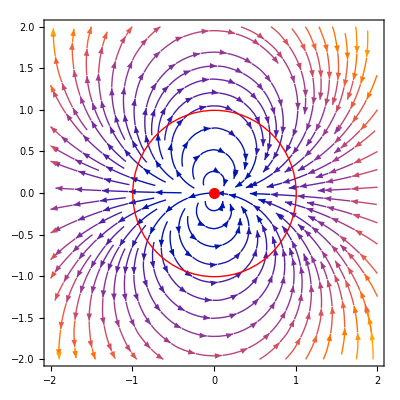

-1

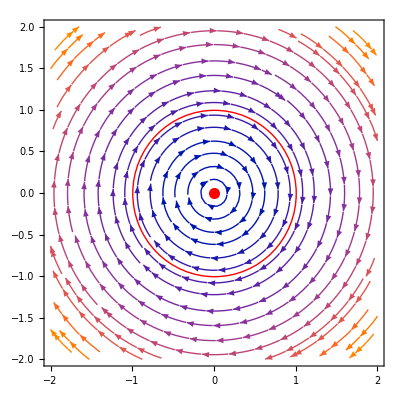

1

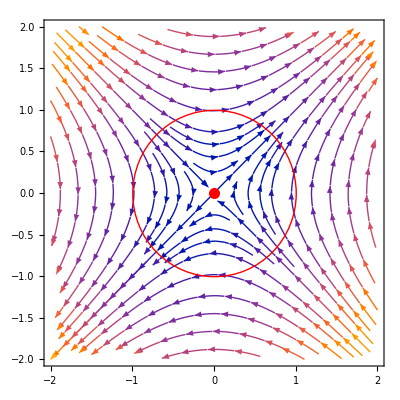

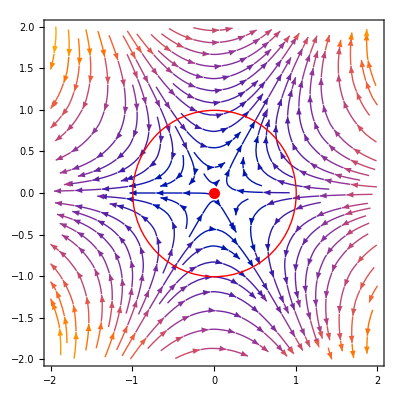

```mathematica
fixedPoint={0,0};
radius=1;
n=-2
StreamPlot[{(x^2+y^2) Abs[n]/2 Cos[n ArcTan[y,x]],(x^2+y^2) Abs[n]/2 Sin[n ArcTan[y,x]]},{x,-2,2},{y,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
n=-1
StreamPlot[{(x^2+y^2) Abs[n]/2 Cos[n ArcTan[y,x]],(x^2+y^2) Abs[n]/2 Sin[n ArcTan[y,x]]},{x,-2,2},{y,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
n=1
StreamPlot[{(x^2+y^2) Abs[n]/2 Cos[n ArcTan[y,x]],(x^2+y^2) Abs[n]/2 Sin[n ArcTan[y,x]]},{x,-2,2},{y,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
n=2; (*Define the value of n*)

StreamPlot[{(x^2+y^2) Abs[n]/2 Cos[n ArcTan[y,x]],(x^2+y^2) Abs[n]/2 Sin[n ArcTan[y,x]]},{x,-2,2},{y,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
n=3; (*Define the value of n*)

StreamPlot[{(x^2+y^2) Abs[n]/2 Cos[n ArcTan[y,x]],(x^2+y^2) Abs[n]/2 Sin[n ArcTan[y,x]]},{x,-2,2},{y,-2,2},Epilog->{Red,PointSize[0.02],Point[fixedPoint],Circle[fixedPoint,radius]}]
```

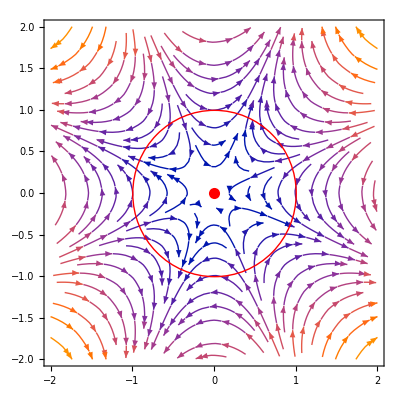

The index is increases proportional to n. Therefore index = n